```mathematica
f[x_]:=x^2-Sin[x]-3
```

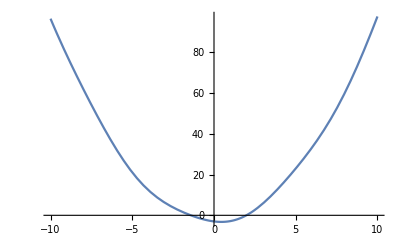

```mathematica
Plot[f[x],{x,-10,10}]
```

```mathematica
FindRoot[f[x]==0,{x,2}]
```

{x→1.97932}

```mathematica
x1r=1.979320146556;
```

```mathematica
FindRoot[f[x]==0,{x,-1}]
```

{x→-1.41831}

```mathematica
x2r=-1.41831009162;
```

```mathematica
x0=1;
```

```mathematica
c=(-1/D[f[x],x]/.x->x0)//N
```

-0.685073

```mathematica
ϕ[x_]:=x-1/(2 x-Cos[x]) *f[x]
```

```mathematica
x1=ϕ[x0]//N
```

2.94662

```mathematica
x2=ϕ[x1]//N
```

2.14816

```mathematica
x3=ϕ[x2]//N
```

1.98776

```mathematica
x4=ϕ[x3]//N
```

1.97934

```mathematica
f[1.9793438420589529]
```

0.000103216

```mathematica
Abs[x1r-x4]<1/2 10^-3
```

True

```mathematica
x0=-2;
```

```mathematica
c=(-1/D[f[x],x]/.x->x0)//N
```

0.279029

```mathematica
ϕ[x_]:=x-1/(2 x-Cos[x]) *f[x]
```

```mathematica
x1=ϕ[x0]//N
```

-1.46725

```mathematica
x2=ϕ[x1]//N
```

-1.41871

```mathematica
x3=ϕ[x2]//N
```

-1.41831

```mathematica
Abs[x2r-x3]<1/2 10^-3
```

```mathematica
f[-1.4183101183019007]
```

7.97317×10^-8

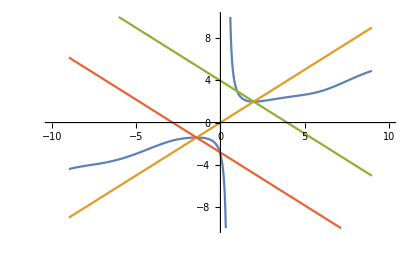

```mathematica
Plot[{ϕ[x],x,-x+2 x1r ,-x+2x2r},{x,-9,9},PlotRange->{{-10,10},{-10,10}}]
```